```mathematica
allGraphs=Association[];
```

```mathematica
veryEmptyMat={{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}}
```

{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}}

```mathematica
(*Monitor[ComputeGraph[veryEmptyMat,16],{globalDepth,Length[allGraphs]}]*)
```

```mathematica
ForceZero[key_]:=Block[{result=0},
If[ToString[allGraphs[key,"comp"]]≠"Equal",
If[ToString[allGraphs[key,"comp"]]=="Greater",
Print["Problem with key ", key];
Interrupt[];
];
allGraphs[key,"comp"]=Equal;
allGraphs[key,"compwhy"]="forced to zero (recursive)";
result+=1;
];
Table[
result+=ForceZero[child]
,{child,Flatten[allGraphs[key,"children"]]}
];
result
];
```

```mathematica
Monitor[ComputeGraph[veryEmptyMat,16],{globalDepth,Length[allGraphs]}]
```

0

```mathematica
Length[allGraphs]
```

1895

```mathematica
alfaKey=35977;
betaKey=31681;
gammaKey=23041 ;
deltaKey=20803;
epsilonKey=27259;
alfa1Key=36166;
beta1Key=31738;
gamma1Key=29608;
delta1Key=36112;
epsilon1Key=31714;
lambdaKey=20665;
k5Key=29524;
```

```mathematica
Table[allGraphs[k,"comp"],{k,Keys[allGraphs]}]//Tally
```

{{Greater,1694},{GreaterEqual,200},{Equal,1}}

```mathematica
(*Table[ForceZero[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]*)
```

## Now compute the inequalities

```mathematica
ineqsPure=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
ineqsSimplified=AndToTable[Simplify[Fold[And,ineqsPure]]];
```

```mathematica
repZero=Map[#[[1]]->#[[2]]&,Select[ineqsSimplified,ToString[#[[0]]]=="Equal"&&Length[DeleteDuplicates[ListofVars[#]]]==1&]]
```

{v1x2x3x4x5→0}

```mathematica
fullVariables=Map[First,repZero]
```

{v1x2x3x4x5}

```mathematica
repcolofour5textBase=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k],If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
repcolofour5graph=Table[allGraphs[k,"colofour"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold,If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
ineqsSimplified
```

{v12345>0,v1234x5>0,v1235x4>0,v123x45>0,v123x4x5>0,v1245x3>0,v124x35≥0,v124x3x5≥0,v125x34>0,v125x3x4>0,v12x345>0,v12x34x5>0,v12x35x4≥0,v12x3x45>0,v12x3x4x5≥0,v1345x2>0,v134x25≥0,v134x2x5≥0,v135x24≥0,v135x2x4≥0,v13x245≥0,v13x24x5≥0,v13x25x4≥0,v13x2x45≥0,v13x2x4x5≥0,v145x23>0,v145x2x3>0,v14x235≥0,v14x23x5≥0,v14x25x3≥0,v14x2x35≥0,v14x2x3x5≥0,v15x234>0,v15x23x4>0,v15x24x3≥0,v15x2x34>0,v15x2x3x4≥0,v1x2345>0,v1x234x5>0,v1x235x4≥0,v1x23x45>0,v1x23x4x5≥0,v1x245x3≥0,v1x24x35≥0,v1x24x3x5≥0,v1x25x34≥0,v1x25x3x4≥0,v1x2x345>0,v1x2x34x5≥0,v1x2x35x4≥0,v1x2x3x45≥0,v1x2x3x4x5==0,v1x25x34+v1x2x34x5>0,v1x245x3+v1x2x3x45>0,v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0,v1x235x4+v1x23x4x5>0,v15x24x3+v15x2x3x4>0,v14x25x3+v14x2x35+v14x2x3x5>0,v14x235+v14x23x5>0,v14x2x35+v1x24x35+v1x2x35x4>0,v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5>0,v14x23x5+v1x23x4x5>0,v14x235+v1x235x4>0,v13x24x5+v13x25x4+v13x2x4x5>0,v13x245+v13x2x45>0,v135x24+v135x2x4>0,v134x25+v134x2x5>0,v13x2x45+v1x2x3x45>0,v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0,v13x24x5+v1x24x35+v1x24x3x5>0,v13x245+v1x245x3>0,v135x2x4+v15x2x3x4>0,v135x24+v15x24x3>0,v13x2x4x5+v14x2x35+v14x2x3x5+v1x2x35x4+v1x2x3x4x5>0,v134x2x5+v1x2x34x5>0,v13x25x4+v14x25x3+v1x25x3x4>0,v134x25+v1x25x34>0,v13x24x5+v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5>0,v12x35x4+v12x3x4x5>0,v124x35+v124x3x5>0,v124x3x5+v12x3x4x5>0,v124x35+v12x35x4>0}

## Now we are going to use the information in the inequalities to set some graph to positive

```mathematica
PositiveExpressions = Map[First,Select[ineqsSimplified,ToString[#[[0]]]=="Greater"&]]
```

{v12345,v1234x5,v1235x4,v123x45,v123x4x5,v1245x3,v125x34,v125x3x4,v12x345,v12x34x5,v12x3x45,v1345x2,v145x23,v145x2x3,v15x234,v15x23x4,v15x2x34,v1x2345,v1x234x5,v1x23x45,v1x2x345,v1x25x34+v1x2x34x5,v1x245x3+v1x2x3x45,v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v1x235x4+v1x23x4x5,v15x24x3+v15x2x3x4,v14x25x3+v14x2x35+v14x2x3x5,v14x235+v14x23x5,v14x2x35+v1x24x35+v1x2x35x4,v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5,v14x23x5+v1x23x4x5,v14x235+v1x235x4,v13x24x5+v13x25x4+v13x2x4x5,v13x245+v13x2x45,v135x24+v135x2x4,v134x25+v134x2x5,v13x2x45+v1x2x3x45,v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v13x24x5+v1x24x35+v1x24x3x5,v13x245+v1x245x3,v135x2x4+v15x2x3x4,v135x24+v15x24x3,v13x2x4x5+v14x2x35+v14x2x3x5+v1x2x35x4+v1x2x3x4x5,v134x2x5+v1x2x34x5,v13x25x4+v14x25x3+v1x25x3x4,v134x25+v1x25x34,v13x24x5+v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5,v12x35x4+v12x3x4x5,v124x35+v124x3x5,v124x3x5+v12x3x4x5,v124x35+v12x35x4}

```mathematica
Table[
Table[
If[ToString[allGraphs[key,"comp"]]≠"Greater",
Print[key, " was " ,allGraphs[key,"comp"]];
allGraphs[key,"comp"]=Greater;
allGraphs[key,"compwhy"]="Expression " <> ToString[pos] <> " is positive from step 1 ";
]
 ,
{key,Select[Keys[allGraphs],allGraphs[#,"colofour"]==pos&]}
],{pos, PositiveExpressions}]
```

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
base5Keys = Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[base5Keys]
```

52

```mathematica
Table[allGraphs[k,"comp"],{k,base5Keys}]//Tally
```

{{Equal,1},{GreaterEqual,30},{Greater,21}}

```mathematica
goodAtoms=Select[base5Keys,ToString[allGraphs[#,"comp"]]=="Greater"&];Length[goodAtoms]
```

21

```mathematica
Table[allGraphs[k,"colofour"],{k,goodAtoms}]/.repcolofour5graph
```

{-Graphics-v1x2x34529537,-Graphics-v1x23x4529768,-Graphics-v1x234x529857,-Graphics-v1x234529888,-Graphics-v15x2x3430262,-Graphics-v15x23x430496,-Graphics-v15x23430586,-Graphics-v145x2x332441,-Graphics-v145x2332684,-Graphics-v1345x239014,-Graphics-v12x3x4549208,-Graphics-v12x34x549216,-Graphics-v12x34549220,-Graphics-v125x3x449963,-Graphics-v125x3449972,-Graphics-v1245x352232,-Graphics-v123x4x556011,-Graphics-v123x4556012,-Graphics-v1235x456770,-Graphics-v1234x558288,-Graphics-v1234559048}

```mathematica
problematicAtoms=Select[base5Keys,ToString[allGraphs[#,"comp"]]=="GreaterEqual"&];Length[problematicAtoms]
```

30

```mathematica
Table[allGraphs[k,"colofour"],{k,problematicAtoms}]/.repcolofour5graph
```

{-Graphics-v1x2x3x4529525,-Graphics-v1x2x35x429527,-Graphics-v1x2x34x529533,-Graphics-v1x25x3x429551,-Graphics-v1x25x3429560,-Graphics-v1x24x3x529605,-Graphics-v1x24x3529608,-Graphics-v1x245x329633,-Graphics-v1x23x4x529767,-Graphics-v1x235x429797,-Graphics-v15x2x3x430253,-Graphics-v15x24x330334,-Graphics-v14x2x3x531711,-Graphics-v14x2x3531714,-Graphics-v14x25x331738,-Graphics-v14x23x531954,-Graphics-v14x23531984,-Graphics-v13x2x4x536085,-Graphics-v13x2x4536086,-Graphics-v13x25x436112,-Graphics-v13x24x536166,-Graphics-v13x24536194,-Graphics-v135x2x436817,-Graphics-v135x2436898,-Graphics-v134x2x538281,-Graphics-v134x2538308,-Graphics-v12x3x4x549207,-Graphics-v12x35x449210,-Graphics-v124x3x551475,-Graphics-v124x3551478}

```mathematica
allGraphs[alfa1Key,"comp"]
```

GreaterEqual

```mathematica
ColourForKey[allGraphs,alfa1Key]
```

RGBColor[1, 0.5, 0]

```mathematica
allGraphs[alfa1Key,"colofour"]/.repcolofour5graph
```

-Graphics-v13x24x536166

```mathematica
ExpressionToTable[Select[ineqsSimplified,#[[0]]==Greater&]]/.repcolofour5graph
```

-Graphics-v15x23430586>0
-Graphics-v145x2x332441>0
-Graphics-v1x2x34529537>0
-Graphics-v1x234529888>0
-Graphics-v12x34549220>0
-Graphics-v1234559048>0
-Graphics-v15x23x430496>0
-Graphics-v125x3x449963>0
-Graphics-v1x234x529857>0
-Graphics-v12x34x549216>0
-Graphics-v123x4x556011>0
-Graphics-v1234x558288>0
-Graphics-v1345x239014>0
-Graphics-v1245x352232>0
-Graphics-v1235x456770>0
-Graphics-v145x2332684>0
-Graphics-v15x2x3430262>0
-Graphics-v125x3449972>0
-Graphics-v1x23x4529768>0
-Graphics-v12x3x4549208>0
-Graphics-v123x4556012>0
-Graphics-v14x23531984+-Graphics-v14x23x531954>0
-Graphics-v14x23531984+-Graphics-v1x235x429797>0
-Graphics-v13x24536194+-Graphics-v1x245x329633>0
-Graphics-v13x24536194+-Graphics-v13x2x4536086>0
-Graphics-v135x2x436817+-Graphics-v15x2x3x430253>0
-Graphics-v135x2436898+-Graphics-v135x2x436817>0
-Graphics-v134x2x538281+-Graphics-v1x2x34x529533>0
-Graphics-v134x2538308+-Graphics-v134x2x538281>0
-Graphics-v15x24x330334+-Graphics-v15x2x3x430253>0
-Graphics-v14x23x531954+-Graphics-v1x23x4x529767>0
-Graphics-v124x3x551475+-Graphics-v12x3x4x549207>0
-Graphics-v124x3551478+-Graphics-v124x3x551475>0
-Graphics-v135x2436898+-Graphics-v15x24x330334>0
-Graphics-v1x235x429797+-Graphics-v1x23x4x529767>0
-Graphics-v12x35x449210+-Graphics-v12x3x4x549207>0
-Graphics-v1x25x3429560+-Graphics-v1x2x34x529533>0
-Graphics-v1x245x329633+-Graphics-v1x2x3x4529525>0
-Graphics-v124x3551478+-Graphics-v12x35x449210>0
-Graphics-v134x2538308+-Graphics-v1x25x3429560>0
-Graphics-v13x2x4536086+-Graphics-v1x2x3x4529525>0
-Graphics-v13x25x436112+-Graphics-v14x25x331738+-Graphics-v1x25x3x429551>0
-Graphics-v13x24x536166+-Graphics-v1x24x3529608+-Graphics-v1x24x3x529605>0
-Graphics-v14x25x331738+-Graphics-v14x2x3531714+-Graphics-v14x2x3x531711>0
-Graphics-v13x24x536166+-Graphics-v13x25x436112+-Graphics-v13x2x4x536085>0
-Graphics-v14x2x3531714+-Graphics-v1x24x3529608+-Graphics-v1x2x35x429527>0
-Graphics-v14x25x331738+-Graphics-v14x2x3x531711+-Graphics-v1x24x3x529605+-Graphics-v1x25x3x429551+-Graphics-v1x2x3x4x529524>0
-Graphics-v1x24x3529608+-Graphics-v1x24x3x529605+-Graphics-v1x25x3x429551+-Graphics-v1x2x35x429527+-Graphics-v1x2x3x4x529524>0
-Graphics-v13x25x436112+-Graphics-v13x2x4x536085+-Graphics-v1x25x3x429551+-Graphics-v1x2x35x429527+-Graphics-v1x2x3x4x529524>0
-Graphics-v13x24x536166+-Graphics-v13x2x4x536085+-Graphics-v14x2x3x531711+-Graphics-v1x24x3x529605+-Graphics-v1x2x3x4x529524>0
-Graphics-v14x2x3531714+-Graphics-v13x2x4x536085+-Graphics-v14x2x3x531711+-Graphics-v1x2x35x429527+-Graphics-v1x2x3x4x529524>0

## Now compute the inequalities (part II)

```mathematica
ineqsPure=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
ineqsSimplified=AndToTable[Simplify[Fold[And,ineqsPure]]];
```

```mathematica
repZero=Map[#[[1]]->#[[2]]&,Select[ineqsSimplified,ToString[#[[0]]]=="Equal"&&Length[DeleteDuplicates[ListofVars[#]]]==1&]]
```

{v1x2x3x4x5→0}

```mathematica
fullVariables=Map[First,repZero]
```

{v1x2x3x4x5}

```mathematica
repcolofour5textBase=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k],If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
repcolofour5graph=Table[allGraphs[k,"colofour"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold,If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
ineqsSimplified
```

{v12345>0,v1234x5>0,v1235x4>0,v123x45>0,v123x4x5>0,v1245x3>0,v124x35≥0,v124x3x5≥0,v125x34>0,v125x3x4>0,v12x345>0,v12x34x5>0,v12x35x4≥0,v12x3x45>0,v12x3x4x5≥0,v1345x2>0,v134x25≥0,v134x2x5≥0,v135x24≥0,v135x2x4≥0,v13x245≥0,v13x24x5≥0,v13x25x4≥0,v13x2x45≥0,v13x2x4x5≥0,v145x23>0,v145x2x3>0,v14x235≥0,v14x23x5≥0,v14x25x3≥0,v14x2x35≥0,v14x2x3x5≥0,v15x234>0,v15x23x4>0,v15x24x3≥0,v15x2x34>0,v15x2x3x4≥0,v1x2345>0,v1x234x5>0,v1x235x4≥0,v1x23x45>0,v1x23x4x5≥0,v1x245x3≥0,v1x24x35≥0,v1x24x3x5≥0,v1x25x34≥0,v1x25x3x4≥0,v1x2x345>0,v1x2x34x5≥0,v1x2x35x4≥0,v1x2x3x45≥0,v1x2x3x4x5==0,v1x25x34+v1x2x34x5>0,v1x245x3+v1x2x3x45>0,v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0,v1x235x4+v1x23x4x5>0,v15x24x3+v15x2x3x4>0,v14x25x3+v14x2x35+v14x2x3x5>0,v14x235+v14x23x5>0,v14x2x35+v1x24x35+v1x2x35x4>0,v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5>0,v14x23x5+v1x23x4x5>0,v14x235+v1x235x4>0,v13x24x5+v13x25x4+v13x2x4x5>0,v13x245+v13x2x45>0,v135x24+v135x2x4>0,v134x25+v134x2x5>0,v13x2x45+v1x2x3x45>0,v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0,v13x24x5+v1x24x35+v1x24x3x5>0,v13x245+v1x245x3>0,v135x2x4+v15x2x3x4>0,v135x24+v15x24x3>0,v13x2x4x5+v14x2x35+v14x2x3x5+v1x2x35x4+v1x2x3x4x5>0,v134x2x5+v1x2x34x5>0,v13x25x4+v14x25x3+v1x25x3x4>0,v134x25+v1x25x34>0,v13x24x5+v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5>0,v12x35x4+v12x3x4x5>0,v124x35+v124x3x5>0,v124x3x5+v12x3x4x5>0,v124x35+v12x35x4>0}

```mathematica
ineqsSimplifiedWithZero=Select[ineqsSimplified/.{v1x2x3x4x5->0},!TrueQ[#]&]
```

{v12345>0,v1234x5>0,v1235x4>0,v123x45>0,v123x4x5>0,v1245x3>0,v124x35≥0,v124x3x5≥0,v125x34>0,v125x3x4>0,v12x345>0,v12x34x5>0,v12x35x4≥0,v12x3x45>0,v12x3x4x5≥0,v1345x2>0,v134x25≥0,v134x2x5≥0,v135x24≥0,v135x2x4≥0,v13x245≥0,v13x24x5≥0,v13x25x4≥0,v13x2x45≥0,v13x2x4x5≥0,v145x23>0,v145x2x3>0,v14x235≥0,v14x23x5≥0,v14x25x3≥0,v14x2x35≥0,v14x2x3x5≥0,v15x234>0,v15x23x4>0,v15x24x3≥0,v15x2x34>0,v15x2x3x4≥0,v1x2345>0,v1x234x5>0,v1x235x4≥0,v1x23x45>0,v1x23x4x5≥0,v1x245x3≥0,v1x24x35≥0,v1x24x3x5≥0,v1x25x34≥0,v1x25x3x4≥0,v1x2x345>0,v1x2x34x5≥0,v1x2x35x4≥0,v1x2x3x45≥0,v1x25x34+v1x2x34x5>0,v1x245x3+v1x2x3x45>0,v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4>0,v1x235x4+v1x23x4x5>0,v15x24x3+v15x2x3x4>0,v14x25x3+v14x2x35+v14x2x3x5>0,v14x235+v14x23x5>0,v14x2x35+v1x24x35+v1x2x35x4>0,v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4>0,v14x23x5+v1x23x4x5>0,v14x235+v1x235x4>0,v13x24x5+v13x25x4+v13x2x4x5>0,v13x245+v13x2x45>0,v135x24+v135x2x4>0,v134x25+v134x2x5>0,v13x2x45+v1x2x3x45>0,v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x35x4>0,v13x24x5+v1x24x35+v1x24x3x5>0,v13x245+v1x245x3>0,v135x2x4+v15x2x3x4>0,v135x24+v15x24x3>0,v13x2x4x5+v14x2x35+v14x2x3x5+v1x2x35x4>0,v134x2x5+v1x2x34x5>0,v13x25x4+v14x25x3+v1x25x3x4>0,v134x25+v1x25x34>0,v13x24x5+v13x2x4x5+v14x2x3x5+v1x24x3x5>0,v12x35x4+v12x3x4x5>0,v124x35+v124x3x5>0,v124x3x5+v12x3x4x5>0,v124x35+v12x35x4>0}

```mathematica
ExpressionToTable[Select[ineqsSimplified,Length[ListofVars[#]]>1&&#[[0]]==Greater&]]/.repcolofour5graph
```

-Graphics-v14x23531984+-Graphics-v14x23x531954>0
-Graphics-v14x23531984+-Graphics-v1x235x429797>0
-Graphics-v13x24536194+-Graphics-v1x245x329633>0
-Graphics-v13x24536194+-Graphics-v13x2x4536086>0
-Graphics-v135x2x436817+-Graphics-v15x2x3x430253>0
-Graphics-v135x2436898+-Graphics-v135x2x436817>0
-Graphics-v134x2x538281+-Graphics-v1x2x34x529533>0
-Graphics-v134x2538308+-Graphics-v134x2x538281>0
-Graphics-v15x24x330334+-Graphics-v15x2x3x430253>0
-Graphics-v14x23x531954+-Graphics-v1x23x4x529767>0
-Graphics-v124x3x551475+-Graphics-v12x3x4x549207>0
-Graphics-v124x3551478+-Graphics-v124x3x551475>0
-Graphics-v135x2436898+-Graphics-v15x24x330334>0
-Graphics-v1x235x429797+-Graphics-v1x23x4x529767>0
-Graphics-v12x35x449210+-Graphics-v12x3x4x549207>0
-Graphics-v1x25x3429560+-Graphics-v1x2x34x529533>0
-Graphics-v1x245x329633+-Graphics-v1x2x3x4529525>0
-Graphics-v124x3551478+-Graphics-v12x35x449210>0
-Graphics-v134x2538308+-Graphics-v1x25x3429560>0
-Graphics-v13x2x4536086+-Graphics-v1x2x3x4529525>0
-Graphics-v13x25x436112+-Graphics-v14x25x331738+-Graphics-v1x25x3x429551>0
-Graphics-v13x24x536166+-Graphics-v1x24x3529608+-Graphics-v1x24x3x529605>0
-Graphics-v14x25x331738+-Graphics-v14x2x3531714+-Graphics-v14x2x3x531711>0
-Graphics-v13x24x536166+-Graphics-v13x25x436112+-Graphics-v13x2x4x536085>0
-Graphics-v14x2x3531714+-Graphics-v1x24x3529608+-Graphics-v1x2x35x429527>0
-Graphics-v14x25x331738+-Graphics-v14x2x3x531711+-Graphics-v1x24x3x529605+-Graphics-v1x25x3x429551+-Graphics-v1x2x3x4x529524>0
-Graphics-v1x24x3529608+-Graphics-v1x24x3x529605+-Graphics-v1x25x3x429551+-Graphics-v1x2x35x429527+-Graphics-v1x2x3x4x529524>0
-Graphics-v13x25x436112+-Graphics-v13x2x4x536085+-Graphics-v1x25x3x429551+-Graphics-v1x2x35x429527+-Graphics-v1x2x3x4x529524>0
-Graphics-v13x24x536166+-Graphics-v13x2x4x536085+-Graphics-v14x2x3x531711+-Graphics-v1x24x3x529605+-Graphics-v1x2x3x4x529524>0
-Graphics-v14x2x3531714+-Graphics-v13x2x4x536085+-Graphics-v14x2x3x531711+-Graphics-v1x2x35x429527+-Graphics-v1x2x3x4x529524>0

```mathematica
pr=Problems[allGraphs,0]//Sort
```

{283→364,283→445,286→367,286→448,361→364,361→367,442→445,442→448,1012→1093,1012→1174,1012→3199,1012→11947,1066→3253,1066→7627,1066→31684,1066→36058,1090→1093,1090→7657,1146→7707,1146→36138,1171→1174,1171→7738,2470→2551,2470→22315,2473→2554,2473→22318,2548→2551,2548→2554,3172→3199,3172→3253,3172→22990,3172→23044,3196→3199,3196→9763,3250→3253,3250→9844,3277→3280,3277→9844,5350→5377,5350→25168,5374→5377,5374→11950,6844→6925,6844→7006,6922→6925,6922→7657,7003→7006,7003→7738,7303→9490,7303→11677,7306→9493,7306→11680,7330→9517,7330→11704,7384→9571,7384→31441,7387→9574,7387→31444,7411→9598,7411→31468,7546→7627,7546→7735,7546→9733,7546→11920,7573→7654,7573→7735,7573→9760,7573→11947,7576→7657,7576→7738,7576→9763,7576→11950,7624→7627,7624→7657,7651→7654,7651→7657,7704→7707,7704→7738,7732→7735,7732→7738,9031→9112,9031→28876,9109→9112,9109→9844,9487→9490,9487→9493,9514→9517,9514→9763,9568→9571,9568→9574,9595→9598,9595→9844,9730→9733,9730→9763,9757→9760,9757→9763,9811→9814,9811→9844,9838→9841,9838→9844,11674→11677,11674→11680,11701→11704,11701→11950,11917→11920,11917→11950,11944→11947,11944→11950,19780→21967,19780→31444,19966→20047,19966→22315,19969→20050,19969→22318,20020→22207,20020→26581,20020→31684,20020→36058,20044→20047,20044→20050,20044→26605,20044→35353,20452→22639,20452→31468,20506→22693,20506→31441,20521→22708,20521→24895,20524→22711,20524→24898,20530→22717,20530→31465,20533→22720,20533→31468,20548→22735,20548→24922,20557→22744,20557→31492,20685→27246,20685→33807,20686→22873,20686→25141,20686→27247,20686→33808,20694→27255,20694→36003,20695→20776,20695→22882,20695→23044,20695→27256,20695→31711,20695→36004,20712→27273,20712→33834,20721→27282,20721→36030,20748→27309,20748→36057,20749→22936,20749→27310,20749→31684,20749→36058,20764→22951,20764→25138,20764→27325,20764→33889,20766→27327,20766→33888,20767→22954,20767→25141,20767→27328,20767→33889,20772→27333,20772→36084,20773→20776,20773→22960,20773→27334,20773→27340,20773→31708,20773→36085,20775→27336,20775→36084,20785→29533,20785→38281,20794→22981,20794→25168,20794→27355,20794→33916,20803→22990,20803→27364,20803→31738,20803→36112,20812→29560,20812→38308,21886→21967,21886→22318,22126→22207,22126→22315,22153→22234,22153→22315,22156→22237,22156→22318,22203→28764,22203→35325,22204→22207,22204→22237,22204→28765,22204→35326,22206→28767,22206→36057,22230→28791,22230→35352,22231→22234,22231→22237,22231→28792,22231→35353,22233→28794,22233→36084,22284→28845,22284→35406,22287→28848,22287→36138,22312→22315,22312→22318,22312→28873,22312→35434,22612→22639,22612→22693,22612→22990,22612→23044,22636→22639,22636→29197,22636→29446,22636→36004,22662→29223,22662→36030,22681→22708,22681→22735,22684→22711,22684→22981,22690→22693,22690→22717,22690→22744,22690→29257,22846→22873,22846→22981,22855→22882,22855→22936,22855→22990,22855→23044,22870→22873,22870→29431,22870→29446,22870→36004,22872→29433,22872→36003,22878→29439,22878→36003,22879→22882,22879→29440,22879→29446,22879→36004,22881→29442,22881→36003,22899→29460,22899→36030,22908→29469,22908→36030,22924→22951,22924→22981,22927→22954,22927→22981,22932→29493,22932→36057,22933→22936,22933→22960,22933→22990,22933→29494,22933→29527,22933→36058,22935→29496,22935→36057,22953→29514,22953→36084,22959→29520,22959→36084,22962→29523,22962→36084,22964→29525,22964→36086,23013→29574,23013→36138,23016→29577,23016→36138,23041→23044,23041→29602,23041→29608,23041→36166,23072→29633,23072→36194,23689→30253,23689→36817,23770→30334,23770→36898,24868→24895,24868→24922,24871→24898,24871→25168,25111→25138,25111→25168,25114→25141,25114→25168,26500→26581,26500→28876,26524→26605,26524→28873,26527→26608,26527→28876,26578→26581,26578→26605,26578→27340,26578→27364,26986→29173,26986→31441,26989→29176,26989→31444,27010→29197,27010→31465,27013→29200,27013→31468,27036→29223,27036→31492,27067→29254,27067→31441,27070→29257,27070→31444,27082→29269,27082→31465,27085→29272,27085→31468,27091→29278,27091→31465,27094→29281,27094→31468,27109→29296,27109→31492,27118→29305,27118→31492,27219→27246,27219→27273,27220→27247,27220→27355,27228→27255,27228→27282,27228→27309,27228→29577,27229→27256,27229→27310,27229→27364,27229→29416,27229→29605,27229→31684,27244→27325,27244→29431,27244→29602,27244→31708,27252→27333,27252→29439,27252→29602,27252→31708,27253→27334,27253→29440,27253→29602,27253→31708,27259→27340,27259→29446,27259→29608,27259→31714,27298→27325,27298→27355,27300→27327,27300→27355,27301→27328,27301→27355,27306→27309,27306→27333,27306→27340,27306→27364,27307→27310,27307→27334,27307→27340,27307→27364,27580→29767,27580→31954,27610→29797,27610→31984,28683→28764,28683→28845,28684→28765,28684→28873,28686→28767,28686→28848,28687→28768,28687→28876,28710→28791,28710→28873,28711→28792,28711→28873,28713→28794,28713→28876,28714→28795,28714→28876,29170→29173,29170→29176,29170→29197,29170→29305,29242→29269,29242→29296,29245→29272,29245→29542,29251→29254,29251→29257,29251→29278,29251→29305,29404→29431,29404→29542,29406→29433,29406→29460,29407→29434,29407→29542,29412→29439,29412→29469,29412→29493,29412→29574,29413→29416,29413→29440,29413→29446,29413→29494,29413→29551,29413→29602,29415→29442,29415→29469,29415→29496,29415→29577,29417→29525,29417→29633,29485→29512,29485→29542,29487→29514,29487→29542,29488→29515,29488→29542,29506→29533,29506→29560,29737→29767,29737→29797,30172→30253,30172→30334,31438→31441,31438→31444,31438→31465,31438→31492,31681→31684,31681→31708,31681→31714,31681→31738,31924→31954,31924→31984,33076→33157,33076→35434,33130→33157,33130→33916,33780→33807,33780→33834,33781→33808,33781→33916,33861→33888,33861→33916,33862→33889,33862→33916,35244→35325,35244→35406,35245→35326,35245→35434,35271→35352,35271→35434,35272→35353,35272→35434,35976→36003,35976→36030,35976→36057,35976→36138,35977→36004,35977→36058,35977→36112,35977→36166,35978→36086,35978→36194,36736→36817,36736→36898,38254→38281,38254→38308,46939→49207,46939→51475,46942→49210,46942→51478,49204→49207,49204→49210,51472→51475,51472→51478}

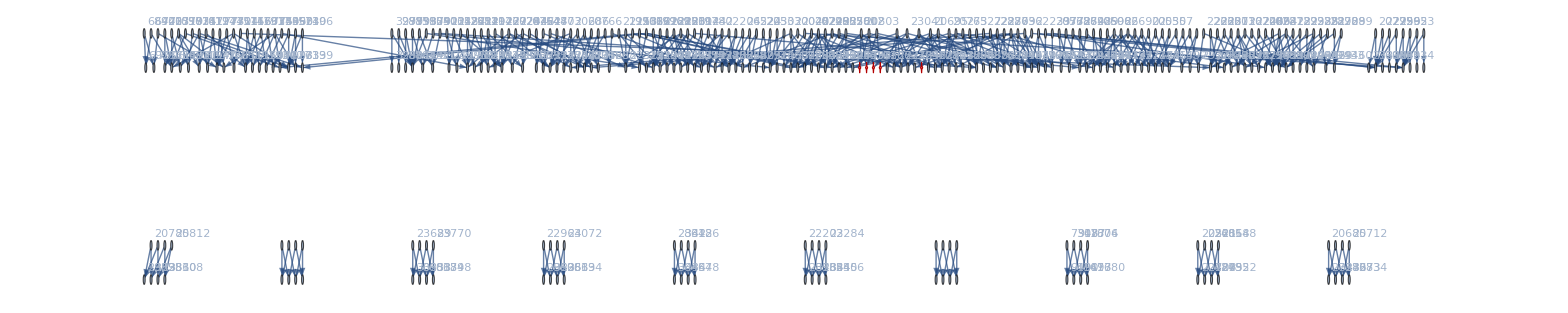

```mathematica
gr2=Graph[pr,VertexLabels->"Name",GraphHighlight->{alfa1Key, beta1Key, gamma1Key, delta1Key, epsilon1Key},GraphHighlightStyle->"VertexConcaveDiamond", GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
WeaklyConnectedComponents[gr2]
```

{{9814,9811,9844,3250,3277,9109,9595,9838,3253,3280,9112,9598,9841,1066,3172,9031,7411,7627,31684,36058,3199,22990,23044,28876,31468,7546,7624,20020,20749,27229,31681,22933,35977,1012,3196,20803,22612,22855,20695,23041,26500,26527,28687,28713,28714,20452,20533,27013,27085,27094,7735,9733,11920,7657,22207,26581,22936,27310,27256,27364,29416,29605,31708,31714,31738,22960,29494,29527,36004,36112,36166,1093,1174,11947,9763,22639,22693,22882,20776,31711,29602,29608,26608,28768,28794,28795,22720,29200,29272,29281,7573,7732,9730,11917,1090,6922,7576,7651,22126,22204,26578,27307,27306,29413,20773,27244,27252,27253,27259,22636,22870,22879,1171,11944,9514,9757,20506,22690,22233,29245,7654,9760,7738,11950,6925,22315,22237,28765,35326,26605,27340,27334,27309,27333,29440,29446,29551,36085,27325,29431,29439,29197,22873,9517,31441,22717,22744,29257,36084,29542,7003,7704,5374,11701,6844,2470,19966,22153,22312,22156,22231,28684,35245,20044,26524,20748,27228,20772,20764,27298,29404,22878,29412,27010,29170,20686,22846,7330,7384,26986,27067,31438,20530,20557,27070,29251,20775,22953,22959,22962,29407,29485,29487,29488,7006,7707,5377,11704,2551,20047,22234,22318,28873,35434,28792,35353,20050,36057,27255,27282,29577,22951,25138,33889,27355,36003,29469,29493,29574,31465,29173,29176,29305,25141,27247,33808,22981,9571,29254,31444,31492,29278,27336,29514,29520,29523,29434,29512,29515,1146,5350,2548,2473,19969,21886,28710,28711,33076,35271,35272,22206,22932,22935,35976,20694,20721,23016,29415,22924,25111,20767,33862,20794,27220,27300,27301,22872,22881,22908,23013,27082,27091,26989,27118,25114,33781,22684,22927,9568,7387,19780,27036,27109,36138,25168,2554,21967,28791,33157,35352,28767,29496,36030,29442,22954,27328,33916,27327,29433,29269,22711,9574,29223,29296,22287,24871,22230,33130,28686,22662,22899,33861,20766,29406,29242,20524,28848,24898,29460,33888},{29417,29525,29633,22964,23072,36086,36194,35978},{28683,28764,28845,22203,22284,35325,35406,35244},{11680,7306,11674,9493,11677,9487,7303,9490},{38281,20785,38254,29533,38308,29506,20812,29560},{22708,20521,22681,24895,22735,24868,20548,24922},{23689,30253,36817,30172,36736,30334,36898,23770},{364,283,361,445,367,442,286,448},{27273,20712,27219,33834,27246,33780,20685,33807},{31924,31954,31984,27580,27610,29767,29797,29737},{49207,46939,49204,51475,49210,51472,46942,51478}}

```mathematica
ToDelete = Flatten[{{29417,29525,29633,22964,23072,36086,36194,35978},{28683,28764,28845,22203,22284,35325,35406,35244},{11680,7306,11674,9493,11677,9487,7303,9490},{38281,20785,38254,29533,38308,29506,20812,29560},{22708,20521,22681,24895,22735,24868,20548,24922},{23689,30253,36817,30172,36736,30334,36898,23770},{364,283,361,445,367,442,286,448},{27273,20712,27219,33834,27246,33780,20685,33807},{31924,31954,31984,27580,27610,29767,29797,29737},{49207,46939,49204,51475,49210,51472,46942,51478}}]
```

{29417,29525,29633,22964,23072,36086,36194,35978,28683,28764,28845,22203,22284,35325,35406,35244,11680,7306,11674,9493,11677,9487,7303,9490,38281,20785,38254,29533,38308,29506,20812,29560,22708,20521,22681,24895,22735,24868,20548,24922,23689,30253,36817,30172,36736,30334,36898,23770,364,283,361,445,367,442,286,448,27273,20712,27219,33834,27246,33780,20685,33807,31924,31954,31984,27580,27610,29767,29797,29737,49207,46939,49204,51475,49210,51472,46942,51478}

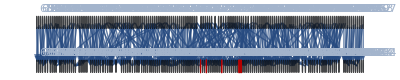

```mathematica
VertexDelete[gr2,ToDelete]
```

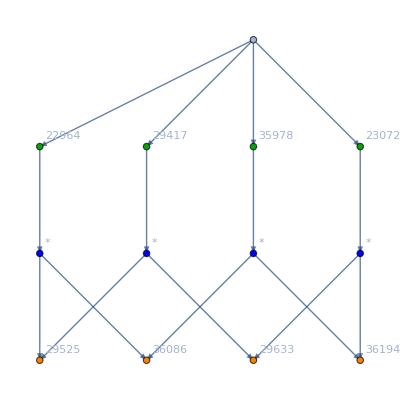

```mathematica
Graph[DependencyGraph[allGraphs,{22964,29417,35978,23072}],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Table[allGraphs[k,"comp"],{k,Keys[allGraphs]}]//Tally
```

{{Greater,1694},{GreaterEqual,200},{Equal,1}}

```mathematica
allGraphs[29524,"colofour"]
```

v1x2x3x4x5

```mathematica
allGraphs["full"]=Association[]
```

<||>

```mathematica
allGraphs["full","graph"]=Graph[{1<->2,2<->3,3<->4,4<->5,1<->5,1<->6,2<->6,3<->6,4<->6,5<->6},VertexLabels->{1->1,2->2,3->3,4->4,5->5},ImageSize->{50,50}, EdgeStyle->Darker[Green], VertexStyle->Red,VertexSize->Small]
```

-Graphics-

```mathematica
allGraphs["full","colofour"]=allGraphs[alfa1Key,"colofour"]+allGraphs[beta1Key,"colofour"]+allGraphs[gamma1Key,"colofour"]+allGraphs[delta1Key,"colofour"]+allGraphs[epsilon1Key,"colofour"]
```

v13x24x5+v13x25x4+v14x25x3+v14x2x35+v1x24x35

```mathematica
allGraphs["full","comp"]=GreaterEqual
```

GreaterEqual

```mathematica
Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5&&EdgeCount[g]==6
&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]
]
&]
```

{27226,22852,20746,20692,20668}

```mathematica
Table[allGraphs[k,"colofour"],{k,{27226,22852,20746,20692,20668}}]
```

{v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5}

```mathematica
Table[Labeled[allGraphs[k,"graph"],Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]]],{k,Select[Keys[allGraphs],MemberQ[ListofVars[allGraphs[#,"colofour"]],v13x25x4]&&allGraphs[#,"comp"]==GreaterEqual&]}]
```

{-Graphics-v13x25x4+v13x2x45+v13x2x4x5,-Graphics-v13x25x4,-Graphics-v13x25x4+v13x2x4x5,-Graphics-v13x245+v13x25x4,-Graphics-v135x2x4+v13x25x4+v13x2x45+v13x2x4x5,-Graphics-v135x2x4+v13x25x4+v13x2x4x5,-Graphics-v134x25+v13x25x4,-Graphics-v134x25+v13x245+v13x25x4,-Graphics-v13x25x4+v1x25x34+v1x25x3x4,-Graphics-v13x25x4+v1x25x3x4,-Graphics-v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x3x4x5,-Graphics-v13x25x4+v1x235x4+v1x25x34+v1x25x3x4,-Graphics-v13x25x4+v1x235x4+v1x25x3x4,-Graphics-v13x25x4+v13x2x4x5+v1x23x4x5+v1x25x3x4+v1x2x3x4x5,-Graphics-v13x25x4+v13x2x4x5+v15x2x3x4+v1x25x3x4+v1x2x3x4x5,-Graphics-v12x3x4x5+v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x3x4x5,-Graphics-v13x24x5+v13x25x4+v14x25x3+v14x2x35+v1x24x35}

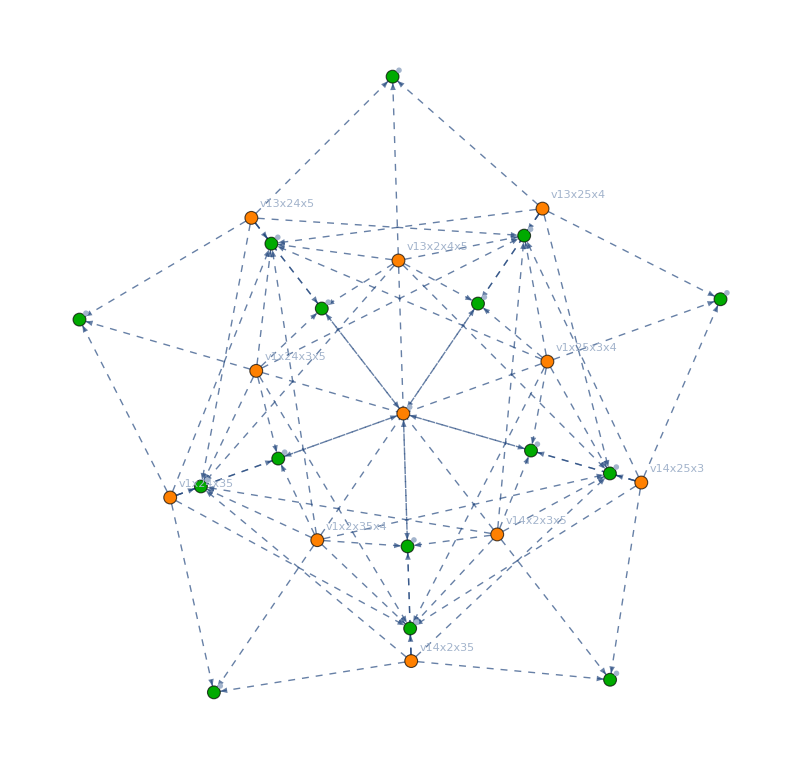

```mathematica
Graph[ExpressionsToGraph6[Join[Map[First,Select[ineqsSimplifiedWithZero,Length[ListofVars[#]]>2&&#[[0]]==Greater&]],{v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5,allGraphs["full","colofour"]}]/.{allGraphs[29524,"colofour"]->0}],GraphLayout->"HighDimensionalEmbedding",ImageSize->800,EdgeStyle->Dashed]
```